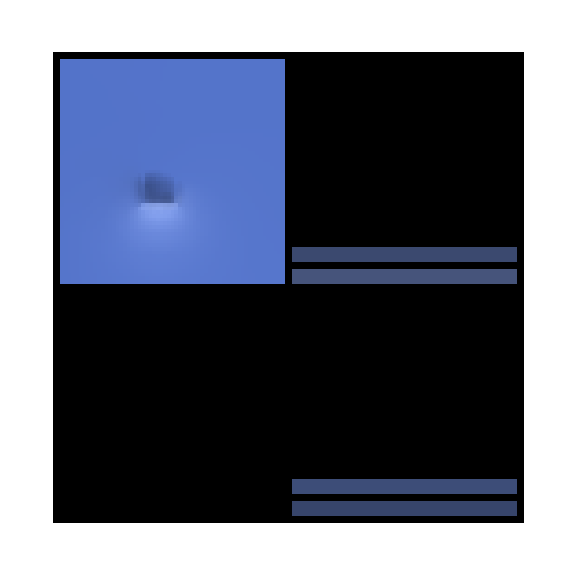

```mathematica
ClearAll[lmData,imgData,imgTable,resx,resy,plotImgTable];

lmData=ToExpression[Import["LQ_Lightmap.pscene"]];
resx=lmData["sizeX"];
resy=lmData["sizeY"];
imgData=lmData["sampleData"];

imgTable=Table[1,resx,resy];

plotImgTable[mul_:1]:=Module[
{i,j},

For[i=1,i≤resx,i++,
For[j=1,j≤resy,j++,
 imgTable[[i]][[j]]=RGBColor[mul*imgData[[(i-1)+(j-1)*resx+1]]];
]
];

ArrayPlot[imgTable]
];



(*Manipulate[
Show[
plotImgTable[mul],
Lighting->{{"Ambient",White}},
Boxed->False, Axes->False,AxesLabel->{"X","Y","Z"}],

{{mul,1},0.1,5}
]*)
Show[plotImgTable[],ImageSize->Large]
```